```mathematica
Limit[1/x, x->∞]
```

0

```mathematica
Limit[1/x,x->0,Direction->-10]
```

∞

```mathematica
D[1/x,x,x]
```

2/x^3

```mathematica
Limit[x^α,x->∞, Assumptions->α≥0]
```

∞

```mathematica
Limit[(1-x)*Sin[π/2*x]/(Cos[π/2*x]),x->1]
```

2/π

```mathematica
Limit[x,x->0]
```

0

```mathematica
Limit[1/x,x->0,Direction->1]
```

-∞

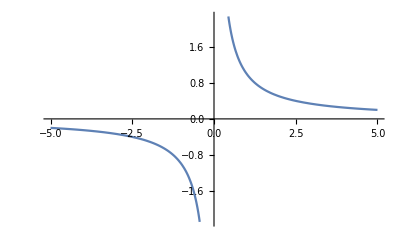

```mathematica
plt=Plot[1/x,{x, -5,5}]
```

```mathematica
Limit[Sin[x],x->∞]
```

Indeterminate

```mathematica
D[Cos[x],x]
```

-Sin[x]

```mathematica
D[Cos[x],x,x]
```

-Cos[x]

```mathematica
Limit[Log[1-2x]/x,x->0]
```

-2

```mathematica
Limit[(D[Log[1-2x],x])/D[x, x],x->0]
```

-2

```mathematica
Limit[(1-x)*Sin[π/2*x]/(Cos[π/2*x]),x->1]
```

2/π

```mathematica
Limit[D[(1-x)*Sin[π/2*x],x]/D[Cos[π/2*x],x],x->1]
```

```mathematica
2/π
```

```mathematica
Limit[Sin[g]/g,g->0]
```

1

```mathematica
Limit[D[Sin[g],g]/D[g,g],g->0]
```

1

```mathematica
Limit[(4 x^3-4 x^2+2x+1)/(x^3+3 x^2+π),x->∞]
```

4

```mathematica
D[(4 x^3-4 x^2+2x+1),x,x,x]/D[(x^3+3 x^2+π),x,x,x] /. x->∞
```

4

```mathematica
Limit[x^α/Log[x],x->∞, Assumptions->α≥0]
```

∞

```mathematica
Limit[D[x^α,x]/D[Log[x],x],x->∞, Assumptions->α≥0]
```

∞

```mathematica
Limit[x^α/Log[x],x->∞, Assumptions->α<0]
```

0

```mathematica
Limit[D[x^α,x]/D[Log[x],x],x->∞, Assumptions->α<0]
```

```mathematica
0

Clear[x,y]
```

0

```mathematica
(*первая функция*)
```

```mathematica
a=x/(CubeRoot[x^2-1])
```

x/((-1+x^2)^(1/3))

```mathematica
FunctionDomain[a,x]
```

```mathematica
x<-1||-1<x<1||x>1
(*область определения все вещественные числа кроме -1 и 1*)
```

```mathematica
FunctionRange[a,x,y]
```

```mathematica
True
(*область значений все вещественные числа)*)
```

```mathematica
Limit[a,x->-1,Direction->-2]
```

∞

```mathematica
∞
(*в точке -1 слева предел функции бесконечность*)
```

```mathematica
Limit[a,x->-1,Direction->10]
```

-∞

```mathematica
(*в точке 1 справа предел функции -бесконечность*)
```

```mathematica
Limit[a,x->1,Direction->-1]
```

```mathematica
∞
(*в точке 1 слева предел функции бесконечность*)
```

```mathematica
Limit[a,x->1,Direction->2]
```

```mathematica
-∞
```

```mathematica
(*в точке 1 справа предел функции -бесконечность*)
Limit[a,x->∞]
```

∞

```mathematica
(*на бесконечности функция стремится к бесконечности*)
Limit[a,x->-∞]
```

```mathematica
-∞
(*на -бесконечности функция стремится к -бесконечности*)
```

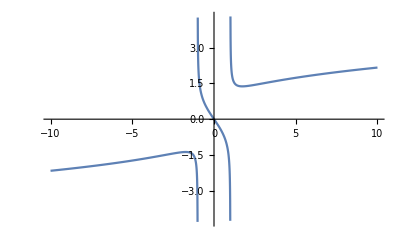

```mathematica
aP=Plot[a,{x,-10,10}]
```

```mathematica
(*функция непериодична, немонотонна на |х|>=1, монотонно убывает на |x|<1 , ее знак постоянный на |х|>=1 (слева знак -, справа +), меняется на |x|<1)
точки разрыва: х=-1 и х=1
точек экстремума нет*)
```

```mathematica
k=Limit[a/x,x->∞]
```

0

```mathematica
b=Limit[a-k*x, x->∞]
```

∞

```mathematica
aAp=Plot[k*x+b,{x,-10,10},PlotStyle->{Red, Dashed}]
Show[aP,aAp]
```

-Graphics-

-Graphics-

```mathematica
(*асимптоты вертикальные х=-1 и х=1 *)
```

```mathematica
(*Вторая функция*)
```

```mathematica
func=(x^2*(x^3-1))/((x^2-4.3)^2*(x^2+1))
```

(x^2 (-1+x^3))/((-4.3+x^2)^2 (1+x^2))

```mathematica
FunctionDomain[func,x]
```

x<-2.07364||-2.07364<x<2.07364||x>2.07364

```mathematica
(*Область определения все вещественные числа кроме -2.073644135332772 и 2.073644135332772 - точки разрыва*)
```

```mathematica
FunctionRange[func,x,y]
```

```mathematica
True
(*функция принимает все вещетвенные значения*)
```

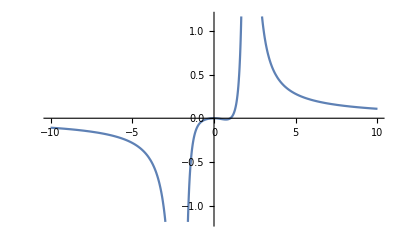

```mathematica
Plot[func,{x,-10,10}]
```

```mathematica
Limit[func,x->-2.073644135332772, Direction->-1]
```

-1.0199×10^31

```mathematica
Limit[func,x->-2.073644135332772, Direction->1]
```

```mathematica
-1.019900968409782*^31
(* в точке разрыва -2.073644135332772 предел функции справа и слева равен -бесконечности*)
```

```mathematica
Limit[func,x->2.073644135332772, Direction->-1]
```

8.14207×10^30

```mathematica
Limit[func,x->2.073644135332772, Direction->1]
```

```mathematica
8.142067200708617*^30
(*в точке разрыва 2.073644135332772 предел функции справа и слева равен -бесконечности*)
Limit[func,x->∞]
```

8.14207×10^30

0.

```mathematica
Limit[func,x->-∞]
```

0.

```mathematica
(*на бесконечностях предел 0 *)
(*функция симметрична относительно у=х, на участках меньше точки разрыва и больше точки разрыва функция монотоно убывает и имеет закопостоянство: слева -, справа +, в середине между точками разрыва функция меняет знак и немонотонна(перегибы)*)
```